{{-1.5708,9.62076×10^-17},{-1.5608,0.0154885},{-1.5508,0.0305532},{-1.5408,0.0452149},{-1.5308,0.0594928},{-1.5208,0.0734042},{-1.5108,0.0869653},{-1.5008,0.100191},{-1.4908,0.113094},{-1.4808,0.125688},{-1.4708,0.137983},{-1.4608,0.149992},{-1.4508,0.161724},{-1.4408,0.173187},{-1.4308,0.184392},{-1.4208,0.195346},{-1.4108,0.206057},{-1.4008,0.216531},{-1.3908,0.226777},{-1.3808,0.236799},{-1.3708,0.246604},{-1.3608,0.256198},{-1.3508,0.265587},{-1.3408,0.274774},{-1.3308,0.283764},{-1.3208,0.292564},{-1.3108,0.301175},{-1.3008,0.309603},{-1.2908,0.317852},{-1.2808,0.325924},{-1.2708,0.333824},{-1.2608,0.341555},{-1.2508,0.34912},{-1.2408,0.356522},{-1.2308,0.363763},{-1.2208,0.370847},{-1.2108,0.377775},{-1.2008,0.384551},{-1.1908,0.391177},{-1.1808,0.397655},{-1.1708,0.403987},{-1.1608,0.410175},{-1.1508,0.416221},{-1.1408,0.422127},{-1.1308,0.427895},{-1.1208,0.433526},{-1.1108,0.439022},{-1.1008,0.444384},{-1.0908,0.449615},{-1.0808,0.454714},{-1.0708,0.459684},{-1.0608,0.464526},{-1.0508,0.469241},{-1.0408,0.47383},{-1.0308,0.478295},{-1.0208,0.482635},{-1.0108,0.486853},{-1.0008,0.490949},{-0.990796,0.494924},{-0.980796,0.498778},{-0.970796,0.502513},{-0.960796,0.506129},{-0.950796,0.509627},{-0.940796,0.513008},{-0.930796,0.516271},{-0.920796,0.519418},{-0.910796,0.522449},{-0.900796,0.525364},{-0.890796,0.528165},{-0.880796,0.53085},{-0.870796,0.533421},{-0.860796,0.535878},{-0.850796,0.53822},{-0.840796,0.540449},{-0.830796,0.542564},{-0.820796,0.544566},{-0.810796,0.546454},{-0.800796,0.548228},{-0.790796,0.549889},{-0.780796,0.551436},{-0.770796,0.552869},{-0.760796,0.554189},{-0.750796,0.555394},{-0.740796,0.556485},{-0.730796,0.557462},{-0.720796,0.558323},{-0.710796,0.559069},{-0.700796,0.559699},{-0.690796,0.560213},{-0.680796,0.560611},{-0.670796,0.56089},{-0.660796,0.561052},{-0.650796,0.561095},{-0.640796,0.561019},{-0.630796,0.560822},{-0.620796,0.560504},{-0.610796,0.560064},{-0.600796,0.559501},{-0.590796,0.558814},{-0.580796,0.558001},{-0.570796,0.557062},{-0.560796,0.555995},{-0.550796,0.554798},{-0.540796,0.553471},{-0.530796,0.552012},{-0.520796,0.550418},{-0.510796,0.548689},{-0.500796,0.546822},{-0.490796,0.544816},{-0.480796,0.542667},{-0.470796,0.540375},{-0.460796,0.537936},{-0.450796,0.535348},{-0.440796,0.532608},{-0.430796,0.529714},{-0.420796,0.526662},{-0.410796,0.523449},{-0.400796,0.520071},{-0.390796,0.516525},{-0.380796,0.512807},{-0.370796,0.508912},{-0.360796,0.504836},{-0.350796,0.500574},{-0.340796,0.496121},{-0.330796,0.49147},{-0.320796,0.486616},{-0.310796,0.481553},{-0.300796,0.476272},{-0.290796,0.470766},{-0.280796,0.465028},{-0.270796,0.459047},{-0.260796,0.452813},{-0.250796,0.446315},{-0.240796,0.439542},{-0.230796,0.43248},{-0.220796,0.425113},{-0.210796,0.417426},{-0.200796,0.4094},{-0.190796,0.401013},{-0.180796,0.392243},{-0.170796,0.383063},{-0.160796,0.373441},{-0.150796,0.363342},{-0.140796,0.352725},{-0.130796,0.341542},{-0.120796,0.329732},{-0.110796,0.317227},{-0.100796,0.303941},{-0.0907963,0.289763},{-0.0807963,0.274558},{-0.0707963,0.258141},{-0.0607963,0.240264},{-0.0507963,0.220573},{-0.0407963,0.198526},{-0.0307963,0.173226},{-0.0207963,0.142956},{-0.0107963,0.103437},{-0.000796327,0.0282099}}

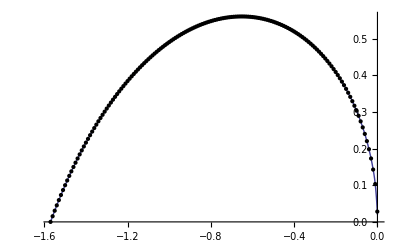

```mathematica
data = Table[{β,ω/.Solve[{1==-ArcTan[β/Abs[ω]]/(√(β^2+ω^2)),ω≥0},{ω},Reals][[1]]},{β,-π/2,0,0.01}]
ifun = Interpolation[data];
Plot[{ifun[β]}, {β,-π/2,0}, PlotRange->{{-π/2,0}},Axes->{True,True}, Epilog->Map[Point,data]]
```